```mathematica
Clear["Global`*"];
```

### Parameter Setup

```mathematica
K=0.3;
m=30;
hbar=2.π/m^2;
per=3;
cutoff=per*m^2;
dim=cutoff;
dq=(2.π)/m;
dp=(2.π)/m;
```

### Objects Setup

```mathematica
iniLis={{1.3,0.9}};
objLis=Flatten[Table[#+{x,y},{x,-dq,dq,dq},{y,-dq,dq,dq}]&/@iniLis,2];
```

### Classical Evolution

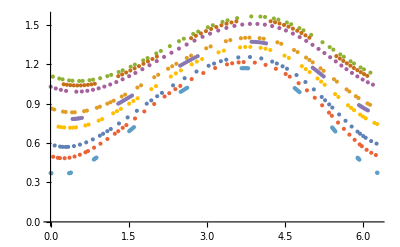

```mathematica
trajLen=100;
{qLis,pLis}={#}&/@Transpose[objLis];
Do[
AppendTo[pLis,Mod[pLis[[-1]]+K*Sin[qLis[[-1]]],2.*π]];
AppendTo[qLis,Mod[qLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}];
tb=Table[Transpose[{qLis[[;;,i]],pLis[[;;,i]]}],{i,1,Length[objLis]}];
objTLis=Table[Transpose[{qLis[[;;,i]],pLis[[;;,i]]}],{i,1,Length[objLis]}];
ListPlot[tb[[;;,1;;50]]]
```

### Quantum Evolution

```mathematica
gaus[x_,{x0_,p0_}]:=Exp[(-(x-x0)^2)/(4.*(2.π/m)^2)+(I(x-x0)*p0)/hbar];
qSpec=Array[(2.π)/dim(#-1.)&,dim];
pSpec=Array[#-1.&,dim]*hbar;
qPhase=Exp[-I K Cos[#]/hbar]&/@qSpec;
pPhase=Exp[-I #^2/(2.*hbar)]&/@pSpec;
q2p[lis_]:=InverseFourier[lis];
p2q[lis_]:=Fourier[lis];
phiLis=ParallelTable[#/Norm[#]&[q2p[gaus[#,obj]&/@qSpec]],{obj,objLis}];
evo[phi_]:=q2p[qPhase*p2q[phi]]*pPhase;
evoPath[ini_]:=Catch[
Block[{path={ini}},
Do[
AppendTo[path,evo[path[[-1]]]];
,{trajLen}
];
Throw[path]
]
];
SetSharedVariable[phiTLis];
phiTLis=ParallelMap[evoPath[#]&,phiLis];
(*Phase Space Representation*)
(*Return a 2-D list, p⟦x,p⟧*)
phi2Ph[phi_]:=Catch[
Block[
{usdphi,res},
res=Table[
usdphi=Table[phi⟦1+(j*m+p)*m;;m+(j*m+p)*m⟧,{j,0,per-1}];
Total[Abs[Fourier[#]]^2&/@usdphi],
{p,0,m-1}
];
Throw[res]
]];
xpGrid=Flatten[Table[{x*2.*π/m,p*2.π/m},{p,0,m-1},{x,0,m-1}],1];
dist[x_,y_]:=Catch[
Block[
{diff=Abs[x-y]},
Throw[Total[Min/@Transpose[{diff,2.*π-diff}]]];
]
];
obj2Ph[obj_]:=Position[xpGrid,SortBy[xpGrid,dist[#,obj]&][[1]]][[1]][[1]];
(*Phase space distribution*)
phiTable=ParallelTable[Flatten[phi2Ph[#]]&/@psi,{psi,phiTLis}];
objTable=ParallelTable[obj2Ph[#]&/@obj,{obj,objTLis}];
dMat=ParallelTable[dist[x,y],{x,xpGrid},{y,xpGrid}];
```

### Save data

```mathematica
(
SetDirectory["/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/KickedRotor/"];
prefix="K="<>ToString[K]<>"_m="<>ToString[m]<>"_1";
If[MemberQ[FileNames[],prefix],Abort[]];
CreateDirectory[prefix];
(*Each line is th(t) or p(t)*)
Export["./"<>prefix<>"/Classical.dat",Join@@Transpose/@objTLis,"Table"];
Do[
Export["./"<>prefix<>"/Quantal"<>ToString[i]<>".dat",phiTable[[i]],"Table"];
Export["./"<>prefix<>"/Class"<>ToString[i]<>".dat",Flatten[objTable[[i]]],"Table"];
,{i,1,Length[objLis]}];
Export["./"<>prefix<>"/xpGrid.dat",xpGrid,"Table"];
Export["./"<>prefix<>"/dMat.dat",dMat,"Table"];
Export["./"<>prefix<>"/PointList.txt",objLis,"Table"];
)
```